$Aborted

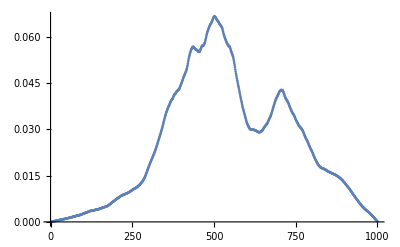

```mathematica
H = DiagonalMatrix[RandomVariate[NormalDistribution[0,.001],10000]];
Do[(
H[[i]][[i + 1]] = 1;
H[[i + 1]][[i]] = 1;
),{i, 1, Length[H] - 1}]
xs = Eigenvectors[H];
ListPlot[xs[[1]], PlotRange->All]
```

```mathematica
Sum[(7-i)(7-j), {i, 6}, {j, 6}]
```

441

```mathematica
D[-2*x*y/(x^2 + y^2)^2, {x, 2}] // FullSimplify
```

(24 x y (-x^2+y^2))/((x^2+y^2)^4)